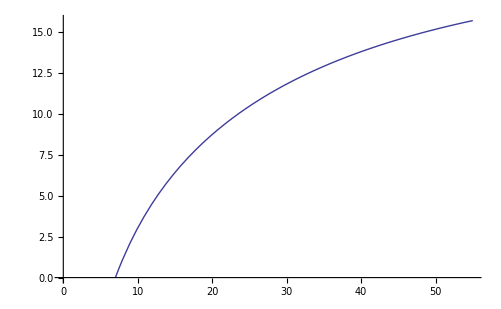

```mathematica
b[f_]:=f^2/(1+10^-4 f^2)
(* frequency f in GHz *)
η[f1_,f2_]:=(b[f1]/b[f2])^(1-1.12*10^-3 √(b[f2]/b[f1])(b[f1])^0.55)
Plot[Abs[10*Log[10,η[7,f]]],{f,7,55},AxesOrigin->{0,0}]
```

```mathematica
10*Log[10,η[7,55]]
```

-15.6788

```mathematica
`
```

```mathematica
(* Free Space loss, f in GHz, d in km *)
LFSL[f_,d_]:= 92.4+20Log[10,f]+20Log[10,d]
Table[{f " GHz",LFSL[f,1100] " db"},{f,10,100,10}]//MatrixForm
```

(10  GHz | 173.228  db
20  GHz | 179.248  db
30  GHz | 182.77  db
40  GHz | 185.269  db
50  GHz | 187.207  db
60  GHz | 188.791  db
70  GHz | 190.13  db
80  GHz | 191.29  db
90  GHz | 192.313  db
100  GHz | 193.228  db)

```mathematica
20 Log[10,50000.]
```

93.9794